```mathematica
ClearAll["Global`*"]
```

```mathematica
p1 = 9.0;
p2 = 10.0;
x2 = {2.0,0.0};
x1 = {1.0,0.0};
xb = {0.0,0.0};
```

```mathematica
r21 = x2-x1;
```

```mathematica
rb1=x1-xb;
```

```mathematica
dpdn = (p2-p1)/Sqrt[Sum[(x2[[i]]-x1[[i]])^2,{i,2}]]
```

1.

```mathematica
pb = dpdn*Sqrt[Sum[rb1[[i]]^2,{i,2}]]
```

1.

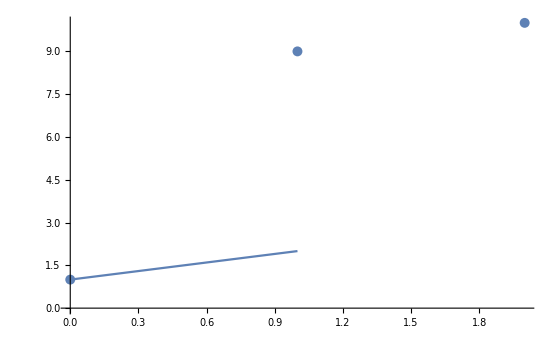

```mathematica
ph1=ListPlot[{{x2[[1]],p2},{x1[[1]],p1},{xb[[1]],pb}}];
ph2=Plot[dpdn*(x)+pb,{x,0,1}];
Show[ph1,ph2]
```

```mathematica
ListPointPlot3D[{{x1[[1]],x1[[2]],p1},{x2[[1]],x2[[2]],p2},{xb[[1]],xb[[2]],pb}}]
```

-Graphics3D-